```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar = RSS;
Hstar = HSS;
Fstar =FSS;
JacSpec = {
{D[dF,F],D[dF,H],D[dF,R]},
{D[dH,F],D[dH,H],D[dH,R]},
{D[dR,F],D[dR,H],D[dR,R]}
};
JacSpecSol = JacSpec/.{R->RSS,H->HSS,F->FSS};
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
(*Can't use analytic version because solution to Hopf must be numerically obtained*)
(*HopfAnalytic = Solve[Det[Sylv]==0,ρ];*)
```

```mathematica
Reps=20;
Opac=0.1;
SM=
ParallelTable[
MassValue=RandomReal[{1,9}]*10^0;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigmavalues=RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-8},B,{n,1,80}];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>(ConsumerGrowth/.M->MassValue)&],
Joined->True,PlotRange->{{10^(-8.5),0.01},{10^(-8.5),0.01}},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->Directive[{Opacity[Opac],ColorData[97,1]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1]}],Line[{{Log@(ConsumerGrowth/.M->MassValue),Log@(10^(-10))},{Log@(ConsumerGrowth/.M->MassValue),Log@1000}}]}]
}],
{Reps}];
LM=
ParallelTable[
MassValue=RandomReal[{1,9}]*10^7;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigmavalues=RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-8},B,{n,1,80}];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>(ConsumerGrowth/.M->MassValue)&],
Joined->True,PlotRange->{{10^(-8.5),0.01},{10^(-8.5),0.01}},Frame->True,PlotStyle->Directive[{Opacity[Opac],ColorData[97,3]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3]}],Line[{{Log@(ConsumerGrowth/.M->MassValue),Log@(10^(-10))},{Log@(ConsumerGrowth/.M->MassValue),Log@1000}}]}]
}],
{Reps}];
```

Greater::nord: Invalid comparison with -2.9534×10^-7-1.43715×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -2.9534×10^-7+1.43715×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -6.12417×10^-7-7.06153×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.46703×10^-7-1.83757×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -2.46703×10^-7+1.83757×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -6.13876×10^-7-3.32031×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.47087×10^-7-8.66703×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -2.92185×10^-7+6.60001×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -2.47087×10^-7+8.66703×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -2.92185×10^-7-6.60001×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -6.14832×10^-7-4.54924×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -2.9081×10^-7+7.04098×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

NSolve::illcnd: Possible ill-conditioning detected in system. Likely cause is exact or approximate multiplicity. This may cause solutions to suffer from loss of precision. Use of sufficiently large WorkingPrecision may resolve this.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[ρ,1].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[1].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[1.].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Greater::nord: Invalid comparison with -4.91219×10^-7+2.37964×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -4.91219×10^-7-2.37964×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -4.27945×10^-7+7.13616×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -2.05405×10^-7-1.20879×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.05405×10^-7+1.20879×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -2.95783×10^-7-1.06675×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -3.56606×10^-7-2.34324×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -3.56606×10^-7+2.34324×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -6.99991×10^-7+4.93912×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.94483×10^-7+8.47542×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -2.94483×10^-7-8.47542×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -2.46081×10^-7+1.77402×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -5.95176×10^-8-1.16052×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -5.95176×10^-8+1.16052×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.23416×10^-7-1.87103×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.77679×10^-8+5.10452×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -1.77679×10^-8-5.10452×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -1.78186×10^-8+5.00653×10^-11 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

$Aborted

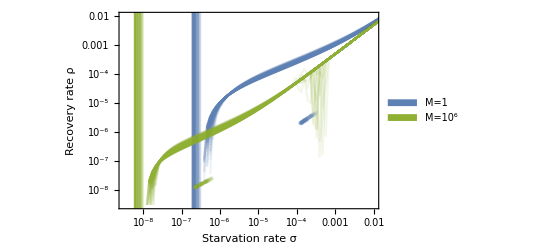

```mathematica
DataHopfPlot=Legended[Show[{
SM,
LM
}],Placed[SwatchLegend[{ColorData[97,1],ColorData[97,3]},{"M=1","M=10^6"},LegendMarkers->"Bubble"],{0.9,0.15}]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_DataHopf.pdf"}],DataHopfPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_DataHopf.pdf